```mathematica
start = {0, 1, 2, 0, 2, 1};
end= {1, 2, 0, 3, 3, 3};
```

```mathematica
λtri = {1 - u - v, u, v};
ϕtri[λ_] := Join[Table[2 λ[[i]](λ[[i]] - 1/2), {i, 1, 3}],Table[4 λ[[start[[i]] + 1]] * λ[[end[[i]] + 1]], {i, 1, 3}]]
```

```mathematica
Plot3D[ϕtri[λtri], {u, 0, 1}, {v, 0, 1}, RegionFunction->Function[{u, v}, u + v ≤ 1],PlotRange->Full, ColorFunction->"TemperatureMap", ImageSize->Full]
```

-Graphics3D-

```mathematica
¬
```

```mathematica
(2 * vol) * Integrate[fTri[λtri], {u, 0, 1}, {v, 0, 1-u}]
```

1/3 vol (c_3+c_4+c_5)

```mathematica
quadrature[f_,coords_,weights_] := 
FullSimplify[Total[MapThread[#2 f[#1]&, {coords, weights}]]];
```

```mathematica
TriQuadratureCoordinates = Table[RotateRight[{2/3, 1/6, 1/6}, n], {n, 0, 2}];
TriQuadratureWeights = Table[vol / 3, {n, 0, 2}];
```

```mathematica
quadrature[fTri, TriQuadratureCoordinates, TriQuadratureWeights]
```

1/3 vol (c_3+c_4+c_5)

```mathematica
λtet = {1 - u - v - w, u, v, w};
ϕtet[λ_] := Join[Table[2λ[[i]](λ[[i]] - 1/2), {i, 1, 4}],Table[4  λ[[start[[i]] + 1]] * λ[[end[[i]] + 1]], {i, 1, 6}]]
```

```mathematica
fTet[λ_] := Total[Table[Subscript[c, i] ϕtet[λ][[i + 1]], {i, 0, 9}]];
```

```mathematica
(6 * vol) * FullSimplify[Integrate[fTet[λtet], {u, 0, 1}, {v, 0, 1-u}, {w, 0, 1 - u - v}]]
```

1/20 vol (-c_0-c_1-c_2-c_3+4 (c_4+c_5+c_6+c_7+c_8+c_9))

```mathematica
TetQuadratureCoordinates = Table[RotateRight[1/ 20 * {5 - Sqrt[5], 5 - Sqrt[5],5 - Sqrt[5],5 + 3*Sqrt[5]}, n], {n, 0, 3}];
TetQuadratureWeights = Table[vol/4, {n, 0, 3}];
```

```mathematica
quadrature[fTet, TetQuadratureCoordinates, TetQuadratureWeights]
```

-1/20 vol (c_0+c_1+c_2+c_3-4 (c_4+c_5+c_6+c_7+c_8+c_9))

```mathematica
λedge = {1 - u, u};
ϕedge[λ_] := Join[Table[2 λ[[i]](λ[[i]] - 1/2), {i, 1, 2}],Table[4 λ[[start[[i]] + 1]] * λ[[end[[i]] + 1]], {i, 1, 1}]];
```

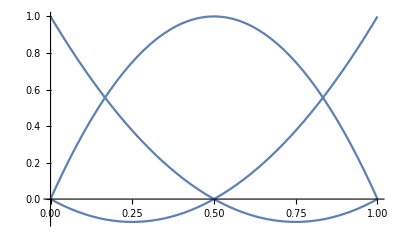

```mathematica
Plot[ϕedge[{1 - u, u}], {u, 0, 1}]
```

```mathematica
fEdge[λ_]:=Total[Table[Subscript[c, i] ϕedge[λ][[i + 1]], {i, 0, 2}]]
```

```mathematica
FullSimplify[Integrate[fEdge[λedge], {u, 0, 1}]]
```

1/6 (c_0+c_1+4 c_2)

```mathematica
EdgeQuadratureCoordinates = 1 / 6 * Table[RotateRight[{3 + Sqrt[3], 3 - Sqrt[3]},n], {n, 0, 1}];
EdgeQuadratureWeights = {vol / 2, vol / 2};
```

```mathematica
quadrature[fEdge, EdgeQuadratureCoordinates, EdgeQuadratureWeights]
```

1/6 vol (c_0+c_1+4 c_2)

TODO : Verify Degree 3 Quadrature Weights.